# 3-species Trophic Chain

```mathematica
Clear["Global`*"]
```

#### Define convenience function for Jacobian

```mathematica
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})
```

#### Specify model

```mathematica
fdRdt[R_,C_,O_]=dRdt=r (1-R/Κ)R -aRC R  C
fdCdt[R_,C_,O_]= dCdt=eRC aRC R C -  aCO C O - mC C
fdOdt[R_,C_,O_]=dOdt= eCO aCO C O - mO O
```

-aRC C R+r R (1-R/Κ)

-C mC-aCO C O+aRC C eRC R

aCO C eCO O-mO O

#### Equilibria

```mathematica
equil=Solve[{ dRdt==0,dCdt==0,dOdt==0},{R,C,O}];
equil//TableForm
```

R→Κ | C→0 | O→0
R→((-aRC mO+aCO eCO r) Κ)/(aCO eCO r) | C→mO/(aCO eCO) | O→-(aCO eCO mC r+aRC^2 eRC mO Κ-aCO aRC eCO eRC r Κ)/(aCO^2 eCO r)
R→mC/(aRC eRC) | C→(r (-mC+aRC eRC Κ))/(aRC^2 eRC Κ) | O→0
R→0 | C→mO/(aCO eCO) | O→-mC/aCO
R→0 | C→0 | O→0

```mathematica
(* Isoplanes *)
```

```mathematica
isoCR=Solve[dRdt==0,C]
isoRC=Solve[dCdt==0,R]
isoCO=Solve[dOdt==0,C]
```

{{C→-(r (R-Κ))/(aRC Κ)}}

{{R→(mC+aCO O)/(aRC eRC)}}

{{C→mO/(aCO eCO)}}

```mathematica
parms={Κ->3,r-> 0.4,aRC->0.1,aCO->0.05,eRC->0.8,eCO->0.5,mC->0.06,mO->0.04};

(* Focal equilibria *)
TableForm[equil/.parms]
```

R→3 | C→0 | O→0
R→1.8 | C→1.6 | O→1.68
R→0.75 | C→3. | O→0
R→0 | C→1.6 | O→-1.2
R→0 | C→0 | O→0

```mathematica
pIso=ContourPlot3D[
{{fdRdt[R,C,O]/.parms}==0,
{fdCdt[R,C,O]/.parms}==0,
{fdOdt[R,C,O]/.parms}==0},
{R,0,3},{C,0,3},{O,0,3},
Axes->True,
AxesLabel->{"R","C","O"},
Mesh->None];
```

```mathematica
pPtEq=Graphics3D[{Red,Sphere[equil[[2,All,2]]/.parms,0.1]}];
Show[pIso,pPtEq]
```

-Graphics3D-

#### Community matrix

```mathematica
A=JacobianMatrix[{dRdt,dCdt,dOdt},{R,C,O}]//FullSimplify;
 (* Evaluated at each equilibrium *)
Aeq1=A/.equil[[1,All]]//FullSimplify;
Aeq2=A/.equil[[2,All]]//FullSimplify;
Aeq3=A/.equil[[3,All]]//FullSimplify;

Aeq1//MatrixForm
```

(-r | -aRC Κ | 0
0 | -mC+aRC eRC Κ | 0
0 | 0 | -mO)

## Carrying capacity 'Κ' as control parameter

```mathematica
subparms=Delete[parms,1];
```

#### Functions for species-specific equilibria

```mathematica
pEquilR[Κ_]=equil[[All,1,2]]/.subparms//FullSimplify
pEquilC[Κ_]=equil[[All,2,2]]/.subparms//FullSimplify;
pEquilO[Κ_]=equil[[All,3,2]]/.subparms//FullSimplify;
```

{Κ,0.6 Κ,0.75,0,0}

#### Functions for feasible abundances

```mathematica
AllFeas1[Κ_]=AllTrue[Re[equil[[1,All,2]]/.subparms],#≥0&]
AllFeas2[Κ_]=AllTrue[Re[equil[[2,All,2]]/.subparms],#≥0&];
AllFeas3[Κ_]=AllTrue[Re[equil[[3,All,2]]/.subparms],#≥0&];
```

Re[Κ]≥0

```mathematica
AllFeas1[1]
```

True

#### Functions for dominant eigenvalues

```mathematica
pReEig1[Κ_]=Max[Re[Eigenvalues[Aeq1/.subparms]]]
pReEig2[Κ_]=Max[Re[Eigenvalues[Aeq2/.subparms]]];
pReEig3[Κ_]=Max[Re[Eigenvalues[Aeq3/.subparms]]];
```

Max[-0.04,-0.06+0.08 Re[Κ]]

### Plot stable and unstable equilibria as functions of carrying capacity Κ

```mathematica
Κmin=0;Κmax=2.5;
ymin=-0.005;
flabx=0.11;
ELineCols={
{Thick,Green},{Thick,Dashed, Green},
{Thick,Blue},{Thick,Dashed,Blue},
{Thick,Red},{Thick,Dashed,Red}};
```

#### Intermediate consumer

```mathematica
PlotEqC1=Plot[{pEquilC[Κ][[1]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig1[x]<0&&AllFeas1[x]]];
PlotEqC1u=Plot[{pEquilC[Κ][[1]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[2]],RegionFunction->Function[{x},pReEig1[x]>0&&AllFeas1[x]]];

PlotEqC2=Plot[{pEquilC[Κ][[2]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig2[x]<0&&AllFeas2[x]]];
PlotEqC2u=Plot[{pEquilC[Κ][[2]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[4]],RegionFunction->Function[{x},pReEig2[x]>0&&AllFeas2[x]]];

PlotEqC3=Plot[{pEquilC[Κ][[3]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[5]],RegionFunction->Function[{x},pReEig3[x]<0&&AllFeas3[x]]];
PlotEqC3u=Plot[{pEquilC[Κ][[3]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[6]],RegionFunction->Function[{x},pReEig3[x]>0&&AllFeas3[x]]];
```

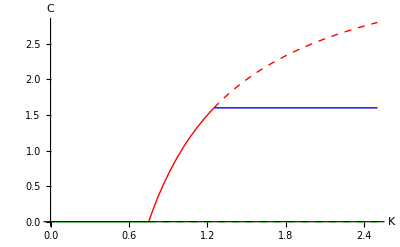

```mathematica
Show[PlotEqC1,PlotEqC1u,  PlotEqC2,PlotEqC2u,  PlotEqC3,PlotEqC3u,  PlotRange->Automatic,AxesLabel->{"K","C"}]
```

#### Top-consumer

```mathematica
PlotEqO1=Plot[{pEquilO[Κ][[1]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig1[x]<0&&AllFeas1[x]]];
PlotEqO1u=Plot[{pEquilO[Κ][[1]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[2]],RegionFunction->Function[{x},pReEig1[x]>0&&AllFeas1[x]]];

PlotEqO2=Plot[{pEquilO[Κ][[2]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig2[x]<0&&AllFeas2[x]]];
PlotEqO2u=Plot[{pEquilO[Κ][[2]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[4]],RegionFunction->Function[{x},pReEig2[x]>0&&AllFeas2[x]]];

PlotEqO3=Plot[{pEquilO[Κ][[3]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[5]],RegionFunction->Function[{x},pReEig3[x]<0&&AllFeas3[x]]];
PlotEqO3u=Plot[{pEquilO[Κ][[3]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[6]],RegionFunction->Function[{x},pReEig3[x]>0&&AllFeas3[x]]];
```

#### Basal resource

```mathematica
PlotEqR1=Plot[{pEquilR[Κ][[1]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig1[x]<0&&AllFeas1[x]]];
PlotEqR1u=Plot[{pEquilR[Κ][[1]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[2]],RegionFunction->Function[{x},pReEig1[x]>0&&AllFeas1[x]]];

PlotEqR2=Plot[{pEquilR[Κ][[2]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig2[x]<0&&AllFeas2[x]]];
PlotEqR2u=Plot[{pEquilR[Κ][[2]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[4]],RegionFunction->Function[{x},pReEig2[x]>0&&AllFeas2[x]]];

PlotEqR3=Plot[{pEquilR[Κ][[3]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[5]],RegionFunction->Function[{x},pReEig3[x]<0&&AllFeas3[x]]];
PlotEqR3u=Plot[{pEquilR[Κ][[3]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[6]],RegionFunction->Function[{x},pReEig3[x]>0&&AllFeas3[x]]];
```

#### Put it all together

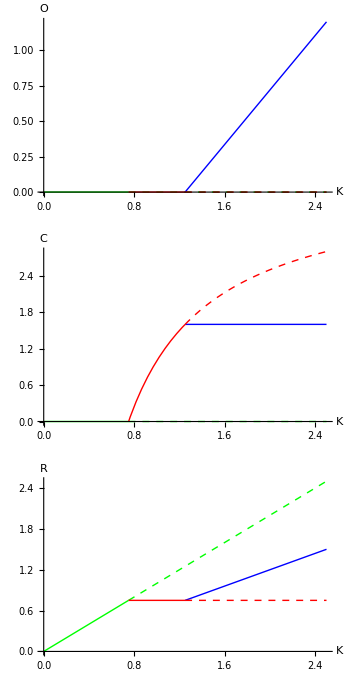

```mathematica
GraphicsGrid[{{
Show[PlotEqO1,PlotEqO1u,  PlotEqO2,PlotEqO2u,  PlotEqO3,PlotEqO3u,  
PlotRange->Automatic,AxesLabel->{"K","O"}]
},{
Show[PlotEqC1,PlotEqC1u,  PlotEqC2,PlotEqC2u,  PlotEqC3,PlotEqC3u,  
PlotRange->Automatic,AxesLabel->{"K","C"}]
},{
Show[PlotEqR1,PlotEqR1u,  PlotEqR2,PlotEqR2u,  PlotEqR3,PlotEqR3u,  
PlotRange->Automatic,AxesLabel->{"K","R"}]
}}]
```

## Analytical invasion criteria

#### Intermediate consumer's invasion threshold in absence of top consumer

Note: top-consumer can't invade resource-only system

```mathematica
RstarC=Solve[dCdt==0,R] /.{O->0} //Flatten
```

{R→mC/(aRC eRC)}

```mathematica
(* When can top-consumer invade RC system at equilibrium in terms of intermediate consumer's abundance? *)
(* Solve Cstar - Cequil ≥0 *)
CstarO=Solve[dOdt==0,C]//Flatten
RCeqC=equil[[3,2,2]]//Expand
RstarO=Solve[CstarO[[1,2]]-RCeqC==0,Κ]//FullSimplify//Flatten
```

{C→mO/(aCO eCO)}

r/aRC-(mC r)/(aRC^2 eRC Κ)

{Κ→-(aCO eCO mC r)/(aRC^2 eRC mO-aCO aRC eCO eRC r)}

```mathematica
pRstarC=ContourPlot[x=={RstarC[[1,2]]/.parms},{x,Κmin,Κmax},{y,0,10},
ContourStyle->{Dashed,Red}];
pRstarO=ContourPlot[x=={RstarO[[1,2]]/.parms},{x,Κmin,Κmax},{y,0,10},
ContourStyle->{Dashed,Blue}];
```

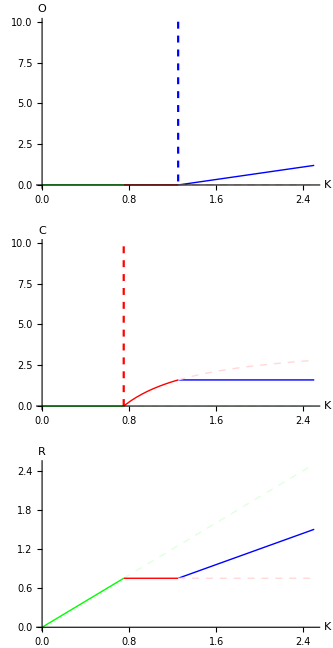

```mathematica
GraphicsGrid[{{
Show[PlotEqO1,PlotEqO1u,  PlotEqO2,PlotEqO2u,  PlotEqO3,PlotEqO3u,
pRstarO,
PlotRange->Automatic,AxesLabel->{"K","O"}]
},{
Show[PlotEqC1,PlotEqC1u,  PlotEqC2,PlotEqC2u,  PlotEqC3,PlotEqC3u, 
pRstarC,
PlotRange->Automatic,AxesLabel->{"K","C"}]
},{
Show[PlotEqR1,PlotEqR1u,  PlotEqR2,PlotEqR2u,  PlotEqR3,PlotEqR3u,  
PlotRange->Automatic,AxesLabel->{"K","R"}]
}}]
```